## 1.2 Properties of Probability

We will begin this section with examples of the concrete construction of probability measures for sample spaces with finitely many outcomes.  With our feet on good intuitive ground, we will then be ready to set up a formal axiom system which permits rigorous proof of some important properties of probability. This is the way that most mathematical research actually proceeds: from concrete to abstract rather than the other way around.

Example 1  If, as we said in Section 1.1, a probability measure gives likelihood to events, then at its most basic level it gives likelihood to simple events, that is, outcomes. As an example, I recently saw a breakdown of advanced placement scores for Illinois 12th graders on the subject test in English Language and Composition.  Scores range from 1 to 5, and the numbers of test takers in these categories for the particular year I looked at were:  1: 74, 2: 293, 3: 480, 4: 254, 5: 130, for a total of 1231 students.  Consider first the random experiment of drawing a student at random from this group and observing the test score.

```mathematica
g1=PieChart[{74,293,480,254,130},ChartLabels->{1,2,3,4,5},ChartStyle->{GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[1]}];
g2=Graphics[Arrow[{{0,0},{.7,.6}}]];
Show[g1,g2,BaseStyle->{FontFamily->"Times",FontSize->10} ]
```

-Graphics-

Figure 1.2 - Sampling from a discrete population

There are 5 possible outcomes, namely, the scores 1-5.  We can think of the experiment of randomly sampling a student score as spinning the arrow on the pie chart of Figure 2, which has been constructed so that the angles of the circular wedges are proportional to the frequencies in the categories that were listed in the last paragraph.  
	This example illustrates several important features of the subject of probability.  First, there is an underlying physics that drives the motion and final resting position of the arrow.  But differences in the starting point, the angular momentum imparted to the arrow, and even slight wind currents and unevenness of the surface of the spinner give rise to a non-deterministic or random phenomenon.  We cannot predict with certainty where the arrow will land. It could be philosophically argued that if we knew all of these randomizing factors perfectly, then the laws of physics would perfectly predict the landing point of the arrow, so that the phenomenon is not really random.  Perhaps this is true in most, if not all, phenomena that we call random.  Nevertheless, it is difficult to know these factors, and the ability to measure likelihoods of events that we model as random is useful to have. 
	Second, this example shows the two main ways of arriving at an assignment of probabilities. We might make simplifying assumptions which lead to a logical assignment of probability.  Or we might repeat the experiment many times and observe how frequently events occur.  We were fortunate enough here to have the background data from which our spinner was constructed, which would indicate by simple counting that if the spinner was truly spun "randomly" we should assign probabilities

P[1]=74/1231, P[2]=293/1231, P[3]=480/1231, P[4]=254/1231, P[5]=130/1231

to the five outcomes.  But step back for a moment and consider what we would have to do with our spinner if we weren't blessed with the numbers.  We would have no recourse but to perform the experiment repeatedly.  If, say, 1000 spins produced 70 1's, then we would estimate P[1] empirically by 70/1000=.07, and similarly for the other outcomes. 
	Third, we can attempt to generalize conclusions.  This data set itself can be thought of as a sort of repeated spinning experiment, in which each student represents a selection from a larger universe of students who could take the test.  The probabilities in formula (1), which would be exact probabilities for the experiment of selecting one student from this particular batch, become estimates of probabilities for a different experiment; that of selecting 1231 students from the universe of all students, past and present, who could take the test.  Whether our particular data set is a "random" sample representing that universe without bias is a very serious statistical question, best left for a statistics course with a good unit on samples and surveys.
	Using the probabilities in (1), how should probability be assigned to composite events like "1 or 3?" The logical thing to do is to pool together the probabilities of all outcomes that are contained in the composite event.  Then we would have

P[1 or 3] = P[1] + P[3] = 74/1231+ 480/1231 = 554/1231

So the probability of an event is the total of all probabilities of the outcomes that make up the event. 
	Two implications follow easily from the last observation: the empty event ∅ which contains no outcomes has probability zero. Also, the event that the spinner lands somewhere is certain, that is, it has probability 1 (100%). Another way to look at it is that the sample space, denoted by Ω say, is the composite event consisting of all outcomes. In this case we have:

P[Ω] | = | P[1 or 2 or 3 or 4 or 5]
  | = | P[1] + P[2]  + ⋯+ P[5]
  | = | 74/1231+293/1231+ ⋯ +130/1231
  | = | 1

In summary, so far we have learned that outcomes can be given probabilities between 0 and 1 using theoretical assumptions or empirical methods, and probabilities for composite events are the totals of the outcome probabilities for outcomes in the event. Also P[∅]=0 and P[Ω]=1. Try the following activity, which suggests another property. You will learn more about that property shortly.

Activity 1  For the spinner experiment we looked at P[1 or 3].  Consider now the two events "at least 3" and "between 1 and 3 inclusive."  What is the probability of the event {"at least 3" or "between 1 and 3 inclusive"}?  How does this probability relate to the individual event probabilities?  Can you deduce a general principle regarding the probability of one event or another occurring?

Sometimes we are interested in the set theoretic complement of an event, i.e., the event that the original event does not occur. Does the probability of the complementary event relate to the probability of the event? For the spinner, look at the events "at least 3" and "less than 3," which are complements. We have, using formula (1):

P[at least 3] = P[3 or 4 or 5] = 480/1231+254/1231+130/1231=864/1231
P[less than 3] = P[1 or 2] =74/1231+293/1231=367/1231

Notice that the two probabilities add to one, that is for these two events E and E^c:

P[E] + P[E^c] = 1

This is not a coincidence. Together E and E^c contain all outcomes, and they have no outcomes in common. The total of their probabilities must therefore equal 1, which is the probability of the sample space.  ■

Example 2. Let's look at another random phenomenon.  Recall from Section 1.1 the experiment of selecting a sequence of two numbers at random from the set {1,2,3,4,5} with no repetition of numbers allowed. Such an ordered selection without replacement is known as a permutation, in this case a permutation of 2 objects from 5.  Mathematica can display all possible permutations as follows.  The command 

				KPermutations[list, k] 

in the KnoxProb7`Utilities` package returns a list of all ordered sequences of length k from the list given in its first argument, assuming that a list member, once selected, cannot be selected again.

```mathematica
Needs["KnoxProb7`Utilities`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Get::noopen: Cannot open Utilities`FilterOptions`.

Needs::nocont: Context Utilities`FilterOptions` was not created when Needs was evaluated.

```mathematica
KPermutations[{1,2,3,4,5},2]
```

{{1,2},{2,1},{1,3},{3,1},{1,4},{4,1},{1,5},{5,1},{2,3},{3,2},{2,4},{4,2},{2,5},{5,2},{3,4},{4,3},{3,5},{5,3},{4,5},{5,4}}

```mathematica
Length[KPermutations[{1,2,3,4,5},2]]
```

20

As the Length output reports, there are 20 such permutations. These 20 are the outcomes that form the sample space of the experiment. The randomness of the drawing makes it quite reasonable to take the theoretical approach to assigning probabilities. Each outcome should have the same likelihood. Since the total sample space has probability 1, the common likelihood of the simple events, say x, satisfies

x + x + ⋯ + x (20 times) = 1 ⟹ 20x=1 ⟹ x=1/20

In other words, our probability measure on the sample space is defined on outcomes as:

P[{1,2}]=P[{2,1}]=P[{1,3}]=⋯=P[{5,4}]=1/20

and for composite events, we can again total the probabilities of outcomes contained in them.

Activity 2  In the example of selecting two positive integers from the first five, find the probability that 1 is in the sample. Explain why your result is intuitively reasonable.

For instance,

P[either 1 or 2 is in the sample]
= P[{1,2},{2,1},{1,3},{3,1},{1,4},{4,1},{1,5},{5,1},{2,3},{3,2},{2,4},{4,2},{2,5},{5,2}]
= 14/20

and

P[2 is not in sample]
=P[{1,3},{3,1},{1,4},{4,1},{1,5},{5,1},{3,4},{4,3},{3,5},{5,3},{4,5},{5,4}] 
=12/20

By counting outcomes you can check that P[2 is in sample] = 8/20, which is complementary to P[2 is not in sample] = 12/20 from above. Also notice that

P[1 in sample] = 8/20=P[2 in sample]

however,

P[1 in sample or 2 in sample] = 14/20≠8/20+8/20

We see that the probability of the event "either 1 is in the sample or 2 is in the sample" is not simply the sum of the individual probability that 1 is in the sample plus the probability that 2 is in it. The reason is that in adding 8/20+8/20 we let the outcomes {1,2} and {2,1} contribute twice to the sum. This overstates the true probability, but we now realize that it is easy to correct for the double count by subtracting 2/20 which is the amount of probability contributed by the doubly counted outcomes. (See Theorem 2 below.)  ◼

Activity 3 Use Mathematica to display the ordered samples of size 3 without replacement from {1,2,3,4,5,6}. What is the probability that 1 is in the sample? What is the probability that neither 5 nor 6 is in the sample?

Armed with the experience of our examples, let us now develop a mathematical model for probability, events, and sample spaces that proceeds from a minimal set of axioms to derive several of the most important basic properties of probability. A few other properties are given in the exercises.

Definition 1.  A sample space Ω of a random experiment is a set whose elements ω are called outcomes.

Definition 2 below is provisional - we will have to be more careful about what an event is when we come to continuous probability.

Definition 2.  An event A is a subset of the sample space Ω, hence an event is a set of outcomes. The collection of all events is denoted by ℋ.

Suppose for example we consider another sampling experiment in which three letters are to be selected at random, without replacement and without regard to order from the set of letters {a,b,c,d}.  The Combinatorica` package in Mathematica (which is loaded automatically when you load KnoxProb7`Utilities`) has the commands

			KSubsets[list, k]              and            Subsets[universe]

which, respectively, return all subsets of size k taken from the given list of objects, and all subsets of the given universal set.  We can use these to find the sample space of the experiment, and the collection of events ℋ:

```mathematica
Ω=KSubsets[{a,b,c,d},3]
```

{{a,b,c},{a,b,d},{a,c,d},{b,c,d}}

```mathematica
ℋ= Subsets[Ω]
```

{{},{{a,b,c}},{{a,b,d}},{{a,c,d}},{{b,c,d}},{{a,b,c},{a,b,d}},{{a,b,c},{a,c,d}},{{a,b,c},{b,c,d}},{{a,b,d},{a,c,d}},{{a,b,d},{b,c,d}},{{a,c,d},{b,c,d}},{{a,b,c},{a,b,d},{a,c,d}},{{a,b,c},{a,b,d},{b,c,d}},{{a,b,c},{a,c,d},{b,c,d}},{{a,b,d},{a,c,d},{b,c,d}},{{a,b,c},{a,b,d},{a,c,d},{b,c,d}}}

Notice that the empty set {} is the first subset of Ω that is displayed; next are the simple events {{a,b,c}}, {{a,b,d}} etc.; next are the two element composite events; and so forth.  
	In all subsequent work we will continue a practice that we have done so far, which is to blur the distinction between outcomes ω, which are members of the sample space, and simple events {ω} which are sets consisting of a single outcome. This will enable us to speak of the "probability of an outcome" when in fact probability is a function on events, as seen in the next definition.

Definition 3.  A probability measure P is a function taking the family of events ℋ to the real numbers such that
	(i) P[Ω] = 1;
	(ii) For all A ∈ ℋ,  P[A] ≥ 0;
	(iii) If A_1, A_2,⋯  is a sequence of pairwise disjoint events then 
			P[A_1∪A_2∪ ⋯ ] =  Σ_i P[A_i]

Properties (i), (ii), and (iii) are called the axioms of probability. Our mathematical model so far corresponds with our intuition: a random experiment has a set of possible outcomes called the sample space, an event is a set of these outcomes, and probability attaches a real number to each event. Axiom (i) requires the entire sample space to have probability 1, axiom (ii) says that all probabilities are non-negative numbers, and axiom (iii) says that when combining disjoint events, the probability of the union is the sum of the individual event probabilities. For finite sample spaces this axiom permits us to just define probabilities on outcomes, and then give each event a probability equal to the sum of its (disjoint) outcome probabilities. We will encounter various ways of constructing probability measures along the way, which we must verify to satisfy the axioms. Once having done so, other properties of probability listed in the theorems below are ours for free. They follow from the axioms alone, and not from any particular construction, which of course is the huge advantage of basing a mathematical model on the smallest possible collection of axioms.

Theorem 1.  If A is an event with complement A^c, then

P[A] + P[A^c]=1

Therefore, P[A] = 1 - P[A^c] and P[A^c]= 1 - P[A].

Proof.  The events A and A^c are pairwise disjoint, by definition of complementation. By the third axiom,

P[A ∪A^c]=P[A] + P[A^c]

Also, A ∪A^c = Ω. By the first axiom, P[Ω] = 1, therefore

1=P[Ω]=P[A ∪A^c]=P[A] + P[A^c].  ■

Theorem 1 was anticipated earlier. It is generally used in cases where the complement of an event of interest is easier to handle than the original event. If we have the probability of one of the two, then we have the other by subtracting from 1. 
	The next result is based on the idea that the total probability of a union can be found by adding the individual probabilities and correcting if necessary by subtracting the probability in the double-counted intersection region.

Theorem 2. If A and B are arbitrary events, then

P[A∪B] = P[A] + P[B] - P[A∩B]

In particular if A and B are disjoint, then

P[A∪B] = P[A] + P[B]

```mathematica
Clear[Ω,A,B];
Graphics[{Line[{{0,0},{0,2},{4,2},{4,0},{0,0}}],
Circle[{3/2,1},2/3],Circle[{5/2,1},2/3],
Text[Style[Ω,Medium],{3.6,1.8}],Text[Style[A,Medium],{1.4,1.4}],Text[Style[B,Medium],{2.6,1.4}],
		Text[Style["A ∩ B",Italic],{2,.1}],
Arrow[{{2,.2},{2,1}}]}]
```

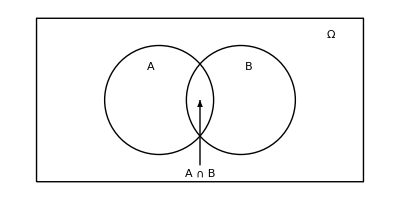

Figure 1.3 - The probability of a union is the total of the event probabilities minus the intersection probability

Proof.  (See Figure 3.) Since A can be expressed as the disjoint union A = (A∩B) ∪ (A∩B^c), and B can be expressed as the disjoint union B=(A∩B) ∪ (B∩A^c) we have, by axiom (iii),

P[A] + P[B] | = | P[A∩B]+P[A∩B^c]+P[A∩B]+P[B∩A^c]
  | = | P[A∩B^c]+P[B∩A^c]+2P[A∩B]

Therefore,

P[A] + P[B] - P[A∩B] = P[A∩B^c]+P[B∩A^c]+P[A∩B]

But it is easy to see from Figure 3 that the events (A∩B^c), (B∩A^c), and (A∩B) are pairwise disjoint and their union is A∪B. Thus, by axiom (iii) of probability again,

P[A∩B^c]+P[B∩A^c]+P[A∩B] = P[A∪B]

Combining (10) and (11) proves the first assertion. The second assertion follows directly as a specialization of axiom (iii) to two events. Alternatively, if A and B are disjoint, then A∩B = ∅ and by Exercise 11, P[∅] = 0. ■

Activity 4  Try to devise an analogous thoerem to Theorem 2 for a three set union. (Hint: if you subtract all paired intersection probabilities, are you doing too much?) See Exercise 14 for a statement of the general result.

You may be curious that the axioms only require events to have non-negative probability. It should also be clear that events must have probability less than or equal to 1, because probability 1 represents certainty. In the exercises you are asked to give a rigorous proof of this fact, stated below as Theorem 3.

Theorem 3.  For any event A, P[A] ≤ 1.  ■

Another intuitively obvious property is that if an event B has all of the outcomes in it that another event A has, and perhaps more, then B should have higher probability than A. This result is given as Theorem 4, and the proof is Exercise 12.

Theorem 4.  If A and B are events such that A ⊂ B, then P[A] ≤ P[B].  ■

Theorems 3 and 4 help to reassure us that our theoretical model of probability corresponds to our intuition, and they will be useful in certain proofs. But Theorems 1 and 2 on complements and unions are more useful in computations. We would like to finish this section by adding a third very useful computational result, usually called the Law of Total Probability. Basically it states that we can "divide and conquer," that is break up the computation of a complicated probability P[A] into a sum of easier probabilities of the form P[A∩B]. The imposition of condition B in addition to A presumably simplifies the computation by limiting or structuring the outcomes in the intersection. (See Figure 4.)  All of our computational results will be used regularly in the rest of the text, and the exercise set for this section lets you begin to practice with them.

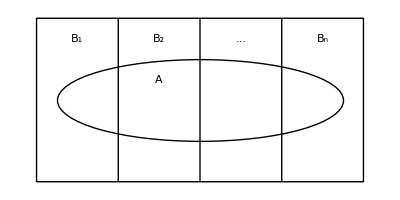

```mathematica
Graphics[{Circle[{4,2},{3.5,1}],
Line[{{0,0},{0,4},{8,4},{8,0},{0,0}}],
Line[{{2,0},{2,4}}],Line[{{4,0},{4,4}}],Line[{{6,0},{6,4}}],
Text[Style[A,Large],{3,2.5}],Text[Subscript[B, 1],{1,3.5}],Text[Subscript[B, 2],{3,3.5}],
			Text["...",{5,3.5}],Text[Subscript[B, n],{7,3.5}]}]
```

Figure 1.4 - The Law of Total Probability

Theorem 5.  Let A be an arbitrary event, and assume that B_1, B_2,B_3, … , B_n is a partition of the sample space Ω, that is, the sets B_i are pairwise disjoint and ∪_(i=1)^n B_i=Ω. Then,

P[A] = ∑_(i=1)^n P[A∩B_i]

Proof.  We will use induction on the number of events B_i beginning with the base case n = 2. In the base case, it is clear that B_2 = B_1^c, and therefore A=(A∩B_1)∪(A∩B_1^c) and the two sets in this union are disjoint. By Theorem 2,

P[A] = P[A∩B_1] + P[A∩B_1^c] = P[A∩B_1] + P[A∩B_2]

The anchor step of the induction is complete.
	Now assume that for all partitions consisting of n events formula (12) is true. Let B_1, B_2,B_3, … , B_(n+1) be a partition of n+1 events; we must show (12) with the upper index of summation replaced by n+1. Define the events C_i by:

C_1=B_1, C_2=B_2, ⋯ ,C_(n-1)=B_(n-1), C_n = B_n∪ B_(n+1)

Then the C_i's are also a partition of Ω (see Activity 5 below). By the inductive hypothesis

P[A] | = | ∑_(i=1)^n P[A∩C_i]
  | = | ∑_(i=1)^(n-1) P[A∩B_i] + P[A∩(B_n∪ B_(n+1))]
  | = | ∑_(i =1)^(n-1) P[A∩B_i] + P[(A∩B_n)∪(A∩B_(n+1))]
  | = | ∑_(i=1)^(n-1) P[A∩B_i] + P[A∩B_n]+P[A∩B_(n+1)]
  | = | ∑_(i=1)^(n+1) P[A∩B_i]

This finishes the inductive step of the proof.  ■

Activity 5  Why are the C_i's in the proof of the Law of Total Probability a partition of Ω?  Why is the fourth line of (13) true?

### Exercises 1.2

1.  Consider the experiment of rolling one red die and two white dice randomly.  Observe the number of the face that lands up on the red die and the sum of the two face up numbers on the white dice.  
  (a) Describe the sample space, giving the format of a typical outcome and two specific examples of outcomes.
  (b) Define a probability measure on this sample space. Argue that it satisfies the three axioms of probability.

2.  This is a continuation of Exercise 1.  A simulated baseball game is played in such a way that each batter has a card like the one shown in the figure.  One red die and two white dice are rolled.  The outcome of the batter's plate appearance is decided by finding the column corresponding to the red die and the row corresponding to the sum of the white dice.  The entry in that row and that column could be a base hit (1b), a double (2b), a triple (3b), a home run (HR) or a blank, which would mean that the batter is out.  For the batter shown, what is the probability that he will get a hit of any kind? If you were designing such a card to simulate a hitter who historically hits about a home run every 20 plate appearances, where would you place HR symbols on the card?

red die
white sum      | 1 | 2 | 3 | 4 | 5 | 6
2 |   |   |   |   |   | 3b
3 | 2b |   | 1b |   |   |  
4 |   |   |   | 1b |   |  
5 |   |   | 1b |   | 2b |  
6 |   |   |   | 1b |   |  
7 |   | 1b |   |   | HR |  
8 | 1b |   |   | 1b |   |  
9 |   | 2b |   |   |   | 1b
10 |   |   |   | 1b |   |  
11 |   |   | 1b |   | 1b |  
12 | 2b |   |   |   |   |

Exercise 2

3.  On a driver's education test there are three questions that are considered most important and most difficult.  The questions are multiple choice, with four alternative answers labeled a, b, c, and d on each question. Exactly one answer is correct for each question.  A test taker guesses randomly on these three questions. 
  (a) Describe the sample space, giving the format of a typical outcome and two specific examples of outcomes.
  (b) Define a probability measure on this sample space. Argue that it satisfies the three axioms of probability.
  (c) What is the probability that the random guesser gets at least two questions right?

4.  (Mathematica) Use Mathematica to display the sample space of all possible random samples without order and without replacement of three names from the list of names {Al, Bubba, Celine, Delbert, Erma}. How many events are in the collection of all events ℋ?  Describe a probability measure for this experiment, and find the probability that either Bubba or Erma is in the sample.

5.  Explain why each of the following attempts P_1 and P_2 is not a good definition of a probability measure on the space of outcomes Ω = {a, b, c, d, e, f, g}.

| P_1 | P_2
a | .12 | .16
b | .05 | .20
c | .21 | .20
d | .01 | .12
e | .04 | .08
f | .28 | .15
g | .13 | .12

6.  (Mathematica) Use Mathematica to display the sample space of all possible random samples in succession and without replacement of two numbers from the set {1,2,...,10}.  Describe a probability measure, and find the probability that 10 is not in the sample.

7.  A 1999 Internal Revenue Service study showed that 44.9 million U.S. taxpayers reported earnings of less than $20,000, 20.4 million earned between $20,000 and $30,000, 16.2 million earned between $30,000 and $40,000, 41.9 million earned between $40,000 and $100,000, and 10.5 million earned more than $100,000.  
  (a) Write the outcomes for the experiment of sampling one taxpayer at random, and define a probability measure. In such a random sample of one taxpayer, what is the probability that the reported earnings is at least $30,000?
  (b) Write the outcomes for the experiment of sampling two taxpayers at random and with replacement, that is, once a taxpayer has been selected that person goes back into the pool and could be selected again.  Define a probability measure.  (Hint: for a succession of two events which do not depend on one another, it makes sense to compute the probability that they both occur as the product of their probabilities.  You can convince yourself of this by considering a very simple experiment like the flip of two coins.)  Find the probability that at least one of the two earned more than $100,000.

8.  Suppose that a point with random x and y coordinates in [-2,2] is selected.  By this we mean that the probability that the random point lies in a region R inside the square is the proportion of the square's area that R has.
  (a) Argue that this means of defining a probability measure on the square [-2,2]×[-2,2] satisfies the axioms of probability.
  (b) Find the probability that the random point will be in the third quadrant.
  (c) Find the probability that the random point is not in the circle of radius 2 shown in the picture.
  (d) Find the probability that the random point is either in the third quadrant or not in the circle of radius 2.

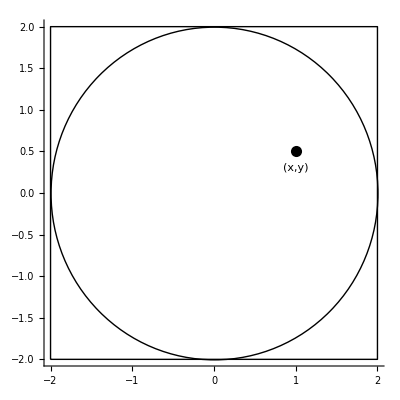

```mathematica
Clear[x,y];
Show[{Graphics[Circle[{0,0},2]],Graphics[Line[{{-2,-2},{-2,2},{2,2},{2,-2},{-2,-2}}]],
	Graphics[{PointSize[.02],Point[{1,.5}]}],
		Graphics[Text[Style["(x,y)",Italic],{1,.3}]]},Axes->True,AspectRatio->1,BaseStyle->{FontSize->8}]
```

Exercise 8

9.  If A and B are events such that P[A∩B] = .24, P[A] = .61, and P[B] = .37, find P[(A∪B)^c].

10. Prove Theorem 3.

11.  Prove that P[∅] = 0.

12.  Prove Theorem 4.

13.  List out all events for the sample space Ω = {ω_1,ω_2,ω_3}.  Find the probability of each simple event if P[{ω_1,ω_2}] = .6, P[{ω_2,ω_3}] = .8, and P[{ω_1,ω_3}] = .6.

14.  Prove that for arbitrary events A, B, and C:

P[A∪B∪C] = P[A] + P[B] + P[C] - (P[A∩B] + P[A∩C] + P[B∩C]) + P[A∩B∩C]

15.  The general result for the probability of a union, which has Theorem 2 and Exercise 14 as special cases, is called the law of inclusion and exclusion. Let A_1, A_2, A_3,..., A_n be a collection of n events.  To simplify notation, let A_ij stand for a typical intersection of two of them A_i∩A_j, let A_ijk stand for a three-fold intersection A_i∩A_j∩A_k, etc. The law states that

P[A_1∪A_2∪A_3∪...∪A_n] 
= Σ_i P[A_i]-Σ_i Σ_(< j)P[A_ij] + Σ_i Σ_(<j)Σ_(<k)P[A_ijk]- ⋯
             + (-1)^(n+1) P[A_1∩A_2∩A_3∩...∩A_n]

In other words, one alternately adds and subtracts all k-fold intersection probabilities as k goes from 1 to n.  Use this result in the following classical problem.  Four men leave their hats at a hat check station, then on departing take a hat randomly.  Find the probability that at least one man takes his own hat.

16.  Recall Exercise 5 of Section 1.1 (the blackjack deal).  Use the Law of Total Probability, Theorem 5, to find P[queen on 2nd] in a well-justified way.

17. There are two groups of experimental subjects, one with 2 men and 3 women and the other with 3 men and 2 women. A person is selected at random from the first group and placed into the second group. Then a person is randomly selected from the second group.  Use the Law of Total Probability to find the probability that the person selected from the second group is a woman.

In this book we will include as appropriate problems taken from the list of sample questions for the Society of Actuaries/Casualty Actuarial Society qualifying exam P (Probability).  These problems have been obtained with permission from the societies at the website  www.soa.org/files/pdf/P-09-05ques.pdf.

Sample Problems from Actuarial Exam P

18. The probability that a visit to a primary care physician's (PCP) office results in neither lab work nor referral to a specialist is 35%. Of those coming to a PCP's office, 30% are referred to specialists and 40% require lab work. Determine the probability that a visit to a PCP's office results in both lab work and referral to a specialist.

19. An urn contains 10 balls: 4 red and 6 blue. A second urn contains 16 red balls and an unknown number of blue balls. A single ball is drawn from each urn.  The probability that both balls are the same color is 0.44.  Calculate the number of blue balls in the second urn.

20. An auto insurance company has 10,000 policyholders. Each policyholder is classified as: (i) young or old; (ii) male or female; and (iii) married or single. Of these policyholders, 3000 are young, 4600 are male, and 7000 are married. The policyholders can also be classified as 1320 young males, 3010 married males, and 1400 young married persons.  Finally, 600 of the policyholders are young married males. How many of the company's policyholders are young, female, and single?

21. An insurer offers a health plan to the employees of a large company. As part of this plan, the individual employees may choose exactly two of the supplementary coverages A, B, and C, or they may choose no supplementary coverage. The proportions of the company's employees that choose coverages A, B, and C are 1/4, 1/3, and 5/12 respectively. Determine the probability that a randomly chosen employee will choose no supplementary coverage.